# Etude de cas: dimensionnement d'une colonne à garnissage

### Paramètres généraux

#### Constantes

```mathematica
R=8.314 (*J/mol K*);
MMco2=44 10^-3 (*kg/mol*);
MMn2=28 10^-3 (*kg/mol*);
MMar=40 10^-3 (*kg/mol*);
MMh2o=18 10^-3 (*kg/mol*);
MMmea=61 10^-3 (*kg/mol*);
gz=9.81 (*m/s^2*);
νmea=2;
```

#### Paramètres opératoires

```mathematica
T=273.15+40 (*K*);
yCO2in=0.1930 (*mol/mol*);
yN2in=0.7167 (*mol/mol*);
yArin=0.0092 (*mol/mol*);
yH2Oin=0.0811 (*mol/mol*);
QgNin=50000 (*Nm^3/h*);
pin=3 10^5 (*Pa*);
αAmine=0.3 (*kg MEA/kg solvant pur*);
θin=0.1 (*mol CO2/mol MEA*);
θout=0.3 (*mol CO2/mol MEA*);
```

#### Composition imposée pour le gaz de sortie

```mathematica
yCO2out=50 10^-6 (*mol/mol*);
```

### Question 1 : détermination du débit de liquide minimum

#### Conversion du débit de gaz à l'entrée en débit massique et masse volumique

```mathematica
MMgazin= yN2in MMn2+yCO2in MMco2+yH2Oin MMh2o+yArin MMar (*kg/mol*);
QGin= QgNin/3600 101325/(R 273.15) MMgazin(*kg/s*);
ρGin= pin/(R T) MMgazin(*kg/m^3*);
```

#### Masse molaire gaz inerte

```mathematica
yinertein=yN2in+yArin+yH2Oin (*mol/mol*);
MMinerte=(yN2in MMn2+yH2Oin MMh2o+yArin MMar)/yinertein (*kg/mol*);
```

#### Composition massique gaz entrée et sortie

```mathematica
xCO2in=(yCO2in MMco2)/(yCO2in MMco2+yinertein MMinerte) (*kg/kg gaz*);

xCO2out=(yCO2out MMco2)/(yCO2out MMco2+(1-yCO2out) MMinerte) (*kg/kg gaz*);
```

#### Bilan gaz

```mathematica
QGout=QGin (1-xCO2in)/(1-xCO2out) (*kg/s*);
Tco2=QGin-QGout (*kg/s*);
```

#### Composition liquide entrée et sortie

```mathematica
xlCarbonein=(αAmine θin MMco2/MMmea)/(1+αAmine θin MMco2/MMmea) (*kg carbone/kg solvant*);
xMEAin=(αAmine (1-νmea θin))/(1+αAmine θin MMco2/MMmea) (*kg MEA libre/kg solvant*);
xlCarboneout=(αAmine θout MMco2/MMmea)/(1+αAmine θout MMco2/MMmea) (*kg carbone/kg solvant*);
xMEAout=(αAmine (1-νmea θout))/(1+αAmine θout MMco2/MMmea) (*kg MEA libre/kg solvant*);
```

#### Bilan liquide

```mathematica
QLin=(Tco2 (1-xlCarboneout))/(xlCarboneout-xlCarbonein) (*kg/s*);
QLout=QLin+Tco2(*kg/s*);
```

#### Résultats

```mathematica
Print["Débit massique de gaz à l'entrée: ",QGin," kg/s - Masse volumique: ",ρGin," kg/m^3"];
Print["Masse molaire du gaz inerte: ",MMinerte," kg/mol"];
Print["Fraction massique dioxyde de carbone gaz entrée: ",xCO2in];
Print["Fraction massique dioxyde de carbone gaz sortie: ",xCO2out];
Print["Débit massique de transfert gaz-liquide de CO_2: ",Tco2," kg/s"];
Print["Fraction massique carbone liquide entrée: ",xlCarbonein];
Print["Fraction massique MEA libre liquide entrée: ",xMEAin];
Print["Fraction massique carbone liquide sortie: ",xlCarboneout];
Print["Fraction massique MEA libre liquide sortie: ",xMEAout];
Print[" "];
Print["Débit de liquide nécessaire à l'entrée: ",QLin," kg/s"];

Print["Débit de liquide à la sortie: ",QLout," kg/s"];
```

Débit massique de gaz à l'entrée: 18.8307 kg/s - Masse volumique: 3.50149 kg/m^3

Masse molaire du gaz inerte: 0.0271318 kg/mol

Fraction massique dioxyde de carbone gaz entrée: 0.279458

Fraction massique dioxyde de carbone gaz sortie: 0.000081083

Débit massique de transfert gaz-liquide de CO_2: 5.26129 kg/s

Fraction massique carbone liquide entrée: 0.021181

Fraction massique MEA libre liquide entrée: 0.234917

Fraction massique carbone liquide sortie: 0.0609606

Fraction massique MEA libre liquide sortie: 0.112685

Débit de liquide nécessaire à l'entrée: 124.198 kg/s

Débit de liquide à la sortie: 129.46 kg/s

### Question2: dimensionnement du diamètre de la colonne

#### Paramètres du garnissage sélectionné : Ceramic Intalox Saddle

```mathematica
dp=25 10^-3 (*m*);
ϵ=0.74 (*m^3 garnissage/m^3 appareil*);
Fp=320 (*m^2/m^3*);
Ap=250 (*m^2/m^3*);
σc=0.061 (*N/m*);
```

#### Paramètres des fluides

```mathematica
ρl=1030.5 (*kg/m^3*);
ρw=992.2 (*kg/m^3*);
μl=1.95 10^-3 (*Pa.s*);
μw=0.653 10^-3 (*Pa.s*);
μg=5.942 10^-5 (*Pa.s*);
σ=69.6 10^-3 (*N/m*);
```

#### Paramètres physico-chimiques du transfert

```mathematica
Dco2g=6.55 10^-8 √T (*m^2/s*);
Dco2l=3 10^-5 Exp[-3096/T] (*m^2/s*);
Dmea=Exp[-15-2200/T](*m^2/s*);
hco2=1.5 10^-5 T Exp[1375/T] (*-*);
kin=10^(7.9-2152/T) (*m^3/(mol*s)*);
```

#### Dimensionnement du diamètre de la colonne

```mathematica
Ql=QLin/ρl (*m^3/s*);
Qg=QGin/ρGin (*m^3/s*);
ΔpOverL=205 (*Pa/m*);
π2=Ql/Qg √(ρl/ρGin);
π1e=Exp[0.1117-4.012 π2^0.25];
 Vsge=√(π1e/(Fp/gz ρGin/ρl ρw/ρl (μl/μw)^0.2)) (*m/s*);
A1=21.79-36.19 π2^0.25+16.60 π2^0.5;
A2=7.06+10.30 π2^0.25-10.36 π2^0.5;
π1Overπ1e=(-49 A1+√((49 A1)^2+98 A2 ΔpOverL))/(98 A2);
VsgOverVsge=√π1Overπ1e;
Vsg=Vsge VsgOverVsge (*m/s*);
Diam=√((4 Qg)/(π Vsg))(*m*);
Ω=(π Diam^2)/4 (*m^2*);
Vsl=Ql/Ω (*m/s*);
```

#### Résultats

```mathematica
Print["Diamètre de la colonne: ",Diam," m"];
Print["Vitesse superficielle du gaz: ",Vsg," m/s"];
Print["Vitesse superficielle du liquide: ",Vsl," m/s"];
If[Vsl≥ 10^-6 Ap (σ/σc)^2,Print["OK - vitesse minimale pour le mouillage atteinte"],Print["Pas OK"]];
```

Diamètre de la colonne: 4.48113 m

Vitesse superficielle du gaz: 0.340995 m/s

Vitesse superficielle du liquide: 0.00764191 m/s

OK - vitesse minimale pour le mouillage atteinte

### Question 3 & 4 : résolution des équations pour le dimensionnement de la hauteur de la colonne

#### Coefficients pour le transfert gaz-liquide sans réaction

```mathematica
kG=(Ap Dco2g) 5.23 (Ap dp)^-2 ((Vsg ρGin)/(μg Ap))^0.7 (μg/(ρGin Dco2g))^0.5 (*m/s*);  
kL=(Ap Dco2l) 0.0051 (Ap dp)^0.4 ((Vsl ρl)/(μl Ap))^1.33 (μl/(ρl Dco2l))^0.5 ((Vsl^2 Ap)/gz)^-0.33 (*m/s*); 
Areacor=Ap (1-Exp[-1.45 (σc/σ)^0.75 ((Vsl ρl)/(μl Ap))^0.1 ((Vsl^2 ρl)/(σ Ap))^0.2 ((Vsl^2 Ap)/gz)^-0.05]) (*m^2/m^3*);
Print["Coefficient transfert gaz: ",kG," m/s"];
Print["Coefficient transfert liquide: ",kL," m/s"];
Print["Densité d'aire interfaciale: ",Areacor," m^2 interface/m^3 lit"];
```

Coefficient transfert gaz: 0.00320015 m/s

Coefficient transfert liquide: 0.0000494406 m/s

Densité d'aire interfaciale: 134.635 m^2 interface/m^3 lit

#### Résolution du système d'équations

```mathematica
p0=pin (*Pa*);
Hf0=15(*m*);
ρg[z]=p[z]/(R T) MMgazin(*kg/m^3*);
kg[z]=(Ap Dco2g) 5.23 (Ap dp)^-2 ((Vsg ρg[z])/(μg Ap))^0.7 (μg/(ρg[z] Dco2g))^0.5 (*m/s*);  
p[z]=p0-ΔpOverL z;
yCO2[z]=(xCO2[z]/MMco2)/(xCO2[z]/MMco2+(1-xCO2[z])/MMinerte);
Hatta[z]=(√(kin (xMEA[z] ρl)/MMmea Dco2l))/kL; (*Eq 9.3*)
N2[z]=(Dmea (xMEA[z] ρl)/MMmea)/(νmea  Dco2l hco2 p[z]/(R T) yCO2[z]); (*Eq 9.4*)
Ac[z]=Hatta[z]/N2[z]+Exp[0.68/Hatta[z]-(0.45 Hatta[z])/N2[z]]; (*Eq. 3.38*)
Eacc[z]=1+Hatta[z]/Ac[z] (1-Exp[-0.65 Hatta[z] √Ac[z]]); (*Eq. 3.37*)
Kgl[z]=(hco2 Eacc[z] kg[z] kL)/(hco2 Eacc[z] kL+kg[z]);
Fco2[z]=Areacor Ω Kgl[z]  p[z]/(R T) yCO2[z] (*mol/(s.m)*);  

EqQgaz=Qgaz'[z]==-MMco2 Fco2[z] (*kg/(s.m)*);
(Qgaz[z+1]-Qgaz[z])/dz=
EqxCO2=xCO2'[z]==-(MMco2 Fco2[z])/Qgaz[z] (1-xCO2[z]) (*kg CO2/(kg gaz.m)*);
EqQliq=Qliq'[z]==-MMco2 Fco2[z] (*kg/(s.m)*);
EqxMEA=xMEA'[z]==Fco2[z]/Qliq[z] (νmea MMmea+xMEA[z] MMco2) (*kg MEA/(kg liq.s)*);
EqxCO2o=xCO2[0]==xCO2in (*kg CO2/kg gaz*);
EqQgazo=Qgaz[0]==QGin  (*kg gaz/s*);
EqQliqo=Qliq[0]==QLout (*kg/s*);
EqxMEAo=xMEA[0]==xMEAout (*kg MEA/kg liq*);
Soluce=NDSolve[{EqQgaz,EqxCO2,EqQliq,EqxMEA,EqxCO2o,EqQgazo,EqQliqo,EqxMEAo},{xCO2[z],Qgaz[z],Qliq[z],xMEA[z]},{z,0,Hf0}];
SolHf=FindRoot[(((xCO2[z]/.(Soluce[[1]]))/.{z->hauteur})-xCO2out)==0,{hauteur,Hf0}];
Hf=hauteur/.SolHf
```

Set::write: Tag Times in (-Qgaz[z]+Qgaz[1+z])/dz is Protected.

14.9697

#### Résultats

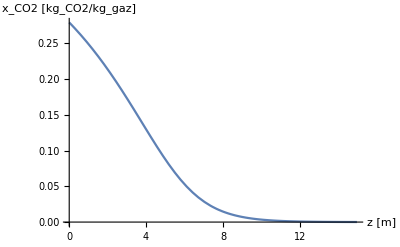

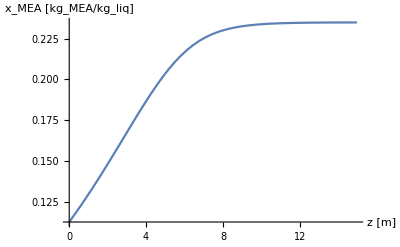

Hauteur requise de la colonne: 14.9697 m

```mathematica
Plot[(xCO2[z]/.(Soluce[[1]])),{z,0,Hf},PlotRange->Full,AxesLabel->{"z [m]","x_CO2 [kg_CO2/kg_gaz]"}]
Plot[(xMEA[z]/.(Soluce[[1]])),{z,0,Hf},PlotRange->Full,AxesLabel->{"z [m]","x_MEA [kg_MEA/kg_liq]"}]
Print["Hauteur requise de la colonne: ",Hf," m"];
```

#### Résultats divers

Débit volumique de liquide requis à l'entrée: 433.88 m^3/h

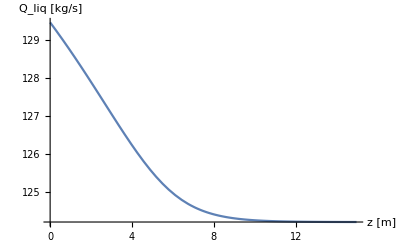

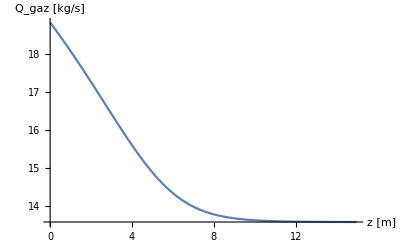

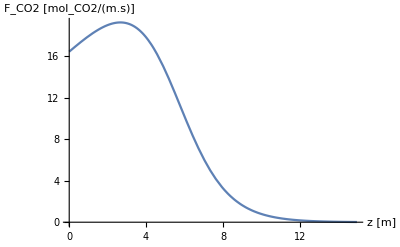

```mathematica
Print["Débit volumique de liquide requis à l'entrée: ",3600 QLin/ρl  ," m^3/h"];
Plot[(Qliq[z]/.(Soluce[[1]])),{z,0,Hf},PlotRange->Full,AxesLabel->{"z [m]","Q_liq [kg/s]"}]
Plot[(Qgaz[z]/.(Soluce[[1]])),{z,0,Hf},PlotRange->Full,AxesLabel->{"z [m]","Q_gaz [kg/s]"}]
Plot[(Fco2[z]/.Soluce[[1]]/.{z->h}),{h,0,Hf},PlotRange->Full,AxesLabel->{"z [m]","F_CO2 [mol_CO2/(m.s)]"}]
```

```mathematica
Plot [{p0-p},{z,0,Hf}]
```

-Graphics-